```mathematica
Clear[src,outp];
src=NotebookDirectory[];
outp=src~~"output\\";
```

## for local use

```mathematica
files=.
files=FileNames[All,src~~"raw-data\\",#]&/@{1,2}; (*01 entfernen*)  
pexaFiles=.
logFiles=.
respFiles=.
pexaFiles=StringCases[files[[2]],__~~".xlsx"]/.{}->Nothing;
logFiles=StringCases[files[[2]],__~~"_protocol.txt"]/.{}->Nothing;
respFiles=StringCases[files[[2]],__~~"Spiro und Diff.tsv"]/.{}->Nothing;
evalfiles=.
evalfiles=Transpose[{Flatten@pexaFiles,Flatten@logFiles,Flatten@respFiles}]
```

{{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\01\2023-03-07 10.01.47.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\01\01_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\01\QHA01 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\02\2023-03-10 09.47.59.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\02\02_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\02\QHA02 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\03\2023-03-10 12.46.27.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\03\03_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\03\QHA03 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\04\2023-03-17 16.23.29.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\04\04_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\04\QHA04 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\05\2023-03-17 18.29.59.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\05\05_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\05\QHA05 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\06\2023-03-21 09.18.10.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\06\06_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\06\QHA06 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\07\2023-03-21 13.03.53.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\07\07_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\07\QHA07 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\08\2023-03-23 09.23.06.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\08\08_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\08\QHA08 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\09\2023-03-23 13.27.18.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\09\09_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\09\QHA09 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\10\2023-03-28 13.24.24.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\10\10_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\10\QHA10 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\11\2023-03-29 09.16.03.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\11\11_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\11\QHA11 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\12\2023-03-29 13.33.25.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\12\12_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\12\QHA12 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\13\2023-04-03 08.40.54.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\13\13_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\13\QHA13 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\14\2023-04-03 10.52.04.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\14\14_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\14\QHA14 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\15\2023-04-04 15.16.01.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\15\15_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\15\QHA15 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\16\2023-04-04 17.53.08.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\16\16_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\16\QHA16 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\17\2023-04-05 10.17.32.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\17\17_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\17\QHA17 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\18\2023-04-05 12.24.27.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\18\18_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\18\QHA18 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\19\2023-04-06 10.27.28.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\19\19_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\19\QHA19 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\20\2023-04-12 09.33.55.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\20\20_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\20\QHA20 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\21\2023-04-12 12.18.05.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\21\21_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\21\QHA21 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\22\2023-04-13 13.26.25.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\22\22_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\22\QHA22 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\23\2023-04-13 15.54.39.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\23\23_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\23\QHA23 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\24\2023-04-14 10.15.38.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\24\24_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\24\QHA24 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\25\2023-04-26 17.50.33.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\25\25_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\25\QHA25 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\26\2023-04-27 14.03.15.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\26\26_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\26\QHA26 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\27\2023-05-02 10.18.41.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\27\27_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\27\QHA27 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\28\2023-05-04 13.40.59.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\28\28_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\28\QHA28 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\29\2023-05-05 13.46.14.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\29\29_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\29\QHA29 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\30\2023-06-06 09.06.49.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\30\30_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\30\QHA30 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\31\2023-06-06 18.20.52.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\31\31_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\31\QHA31 Spiro und Diff.tsv}}

```mathematica
temp=StringReplace[#,{" "->"%20","\\"->"/","C:\\Users\\mona_\\CloudStation\\Forschung\\GitHub\\my-data-storage\\data\\2022_aerosol_quantification\\raw-data"->"https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2022_aerosol_quantification/raw-data","tsv"->"txt"}]&/@evalfiles;
```

```mathematica
Import["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2022_aerosol_quantification/raw-data/31/QHA31%20Spiro%20und%20Diff.tsv"]
```

Import::infer: Cannot infer format of file QHA31%20Spiro%20und%20Diff.tsv.

$Failed

```mathematica
"https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2022_aerosol_quantification/raw-data/16/16_protocol.txt"
"https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2022_aerosol_quantification/raw-data/16/QHA16%20Spiro%20und%20Diff.tsv"
```

```mathematica
(*leere Datenexport-Datei*)
dataexport=.;
dataexport={};
Put[dataexport,outp~~"evaluated Pexa measurements.m"];
```

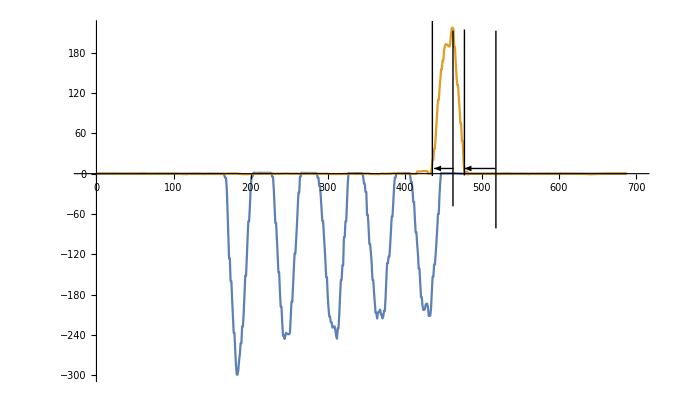
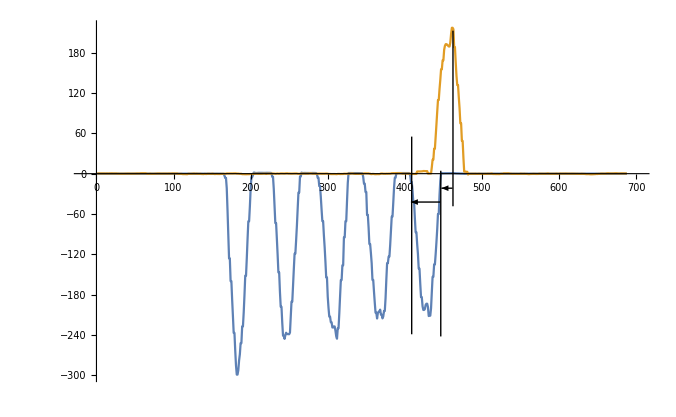
```mathematica
Clear[evaluation]
evaluation[files_List]:=Module[{},

ID=.;
ID=StringCases[files[[1]],"Messungen\\"~~Shortest[a__]~~"\\2023"->a][[1]];

(*Importiere die originialen Daten des Pexa-Messgeräts aus der XLSX-Datei (Blatt 3)*)
dataPEXA=.;
dataPEXA=Import[files[[1]],{"Data",3}];
dataPEXA=Transpose[dataPEXA];

(*Umrechnen der elapsed time auf ms*)
dataPEXA[[2]]=Prepend[Rest@dataPEXA[[2]]*1000,First@dataPEXA[[2]]];


(*Importiere die Protkolldatei*)
dataLOG=.;
dataLOG=Import[files[[2]]];

(*Protokollaufbereitung*)
starttime=. (*in ms*);
x=.;
starttime=ToExpression[StringCases[dataLOG,"PExA Start :: " ~~ Shortest[x__] ~~" ---"->x]][[1]];

times=.;
times=StringCases[dataLOG,"Anmerkungen --- " ~~ x__ ~~ " --- Fragebogen"->x~~" -"];
times=StringReplace[times,", -"->",nv -"];
times=Flatten[StringSplit[times," --- "]];

(*Kommata als versehentliche Trennzeichen in den Kommentarfeldern müssen ersetzt werden *)

r=.;
a=.;
times=Map[(r=StringReverse@StringReplace[StringCases[StringReverse@#,Last@Characters[#]~~ Shortest[a__]~~",0"|",1"->a],","->"***"][[1]];
StringReplace[#,StringReplace[r,"***"->","]->r])&,times];
times= Map[StringSplit[#,","]&,times];
times[[All,1;;-2]]= ToExpression/@times[[All,1;;-2]];

(*die Zeiten werden zur Startzeit synchronisiert, also zur elapsed time synchronisiert*)
times[[All,1]]=times[[All,1]]-starttime;
times[[All,2]]=times[[All,2]]-starttime;

times[[All,-1]]=StringReplace[Last@#,{"***"->",","nv -"->"nv"}]&/@times; (*die Kommata in den Kommentaren werden wieder eingepflegt*)


(*Protokoll-Messabschnitte in dataPEXA finden*)
positions=.;
positions=Partition[Map[FirstPosition[Rest[dataPEXA[[2]]],n_/;n>=#]&,Flatten[times[[All,1;;2]]]],2];
positions=Map[Flatten[#]&,positions,{1}];

(*-Graphics-

"The OPC takes a sample and calculates the particle concentration, that is the primary output from the OPC. The total flow is 0,25l/s , which is what you should use if you are interested of the exhaled particle rather then the particles collected in the impactor." Svante Hojer, from Pexa, 02.01.2023

Partikelgrößen in µm Bins des
11D H20 Aerosolspektrometer Firma Grimm

Bin 1 0,309571553
Bin 2 0,3776321
Bin 3 0,452400811
Bin 4 0,555994647
Bin 5 0,70346326
Bin 6 0,943336729
Bin 7 1,149495579
Bin 8 1,277719573
Bin 9 1,375165427
Bin 10 1,46599766
Bin 11 1,566296996
Bin 12 1,692565199
Bin 13 1,885696842
Bin 14 2,158702163
Bin 15 2,51855379
Bin 16 3,422327161


"This means the first bin is between 0,3096 and 0,3776[µm] and bin 16 contains particles larger then 3,4223[mm]." Svante Hojer

*)

(*Berechnung der Volumina*)
(*Expiratory bounds
-Graphics-
Inspiratory bounds
-Graphics-

Schwelle = 1 bzw -1 m/s
*)

(*Variablenbezeichnungen für die Excel-Output-Datei*)
exportdata=.;
exportdata={{"inspiratory and expiratory target volume [l]","inspiratory volume [ml]","expiratory volume [ml]","equality % [V_expiratory/V_inspiratory / 100]","accuracy variance % [d_exp = V_expiratory - V_target, d_insp = V_inspiratory - V_target; if d_exp = 0 and d_insp = 0 then  0, if d_insp < d_exp or d_exp < d_insp then maximum(|d_exp|, |d_insp|)/ V_target / 100, if (d_exp > 0 and d_insp < 0) or (d_insp > 0 and d_exp < 0) then (|d_exp| + |d_insp|)/ V_target / 100]","inspiratory (target) time [s]","expiratory (target) time [s]","n breaths from HEPA tube before expiration in PExA","volume of breaths before expiration in PExA [ml]","invalid (0 no, 1 yes)","comment (German)","particles > 0.31 - 0.38 µm ± CI[√(n+1)]", "particles 0.38 - 0.45 µm ± CI[√(n+1)]", "particles 0.45 - 0.56 µm ± CI[√(n+1)]", "particles 0.56 - 0.70 µm ± CI[√(n+1)]", "particles 0.70 - 0.94 µm ± CI[√(n+1)]", "particles 0.94 - 1.15 µm ± CI[√(n+1)]", "particles 1.15 - 1.28 µm ± CI[√(n+1)]", "particles 1.28 - 1.38 µm ± CI[√(n+1)]", "particles 1.38 - 1.47 µm ± CI[√(n+1)]", "particles 1.47 - 1.57  µm ± CI[√(n+1)]", "particles 1.57 - 1.69  µm ± CI[√(n+1)]", "particles 1.69 - 1.89  µm ± CI[√(n+1)]", "particles 1.89 - 2.16  µm ± CI[√(n+1)]", "particles 2.16 - 2.52  µm ± CI[√(n+1)]", "particles 2.52 - 3.42  µm ± CI[√(n+1)]", "particles > 3.42  µm ± CI[√(n+1)]", "sum all particles ± CI[√(n+1)]","signal-to-noise-ratio [n/(n+1)]"}};  
exportdataString=exportdata;

(*Variable für die Messabschnitte*)
j=.;
j=0;

(*Schalter für Einschluss/ Ausschluss*)
incl=.;

(*Bildexport*)
tiffexport=.;
tiffexport={};

(*Schleife für die Auswertung der einzelnen Messaufgaben*)
Map[(Clear[particlesextract,extractex,extractins,maxposextract,lbound,ubound,uboundextract,bounds,volexp,volins,lboundins,uboundins,boundsins,extracttime];

(*expiratorische Flussraten*)
extractex=dataPEXA[[3]][[#[[1]];;#[[2]]]];

(*Maximum Exp Flow Position*)
maxposextract=Position[extractex,Max@extractex][[1,1]]; 

(*inspiratorische Flussraten*)
extractins=dataPEXA[[33]][[#[[1]];;#[[2]]]];

(*elapsed time*)
extracttime=dataPEXA[[2]][[#[[1]];;#[[2]]]];

(*Spalte 4 ist Deltatime OPC, 5-20 sind die Partikelklassen*)
particlesextract=dataPEXA[[4;;20]][[All,#[[1]];;#[[2]]]];
particlesextractsum=dataPEXA[[21]][[#[[1]];;#[[2]]]];

(*für die Berechnung der Partikel und Flussraten werden nur Messbereiche genommen, die entweder gültig sind oder im Kommentar "Equa" oder "V " ("Equality" oder "Volume") enthalten*)
(*j=0*)
j=j+1;
Which[times[[j,-2]]==1 && StringContainsQ[times[[j,-1]],"Equa"|"V "],incl=True,times[[j,-2]]==1,incl=False,times[[j,-2]]==0,incl=True];

(*Nur auszuwertende Messbereiche werden verarbeitet*)
If[incl==False,Nothing,

(*die expiratorische Flussrate muss bei > 1 m/s liegen, sonst kann keine Berechnung der Volumina und Partikel erfolgen*)
If[Max@extractex>1,


(*zunächst Bestimmung der Grenzen für expiratory flow rate*)

(*lowerbound: Start der Expiration ist eine Flowrate > 1 m/s*)
lbound=maxposextract-FirstPosition[Reverse[extractex[[1;;maxposextract]]],i_/;i<=1] ;

(*upperbound: wird rückwärts von 5 Sekunden nach Max-Expiratory flow rate bzw. wenn kleiner vom Ende her gesucht*)
uboundextract=extractex[[maxposextract;;(If[maxposextract+50<Length@extractex,maxposextract+50,Length@extractex])]] ;
ubound=maxposextract+Length@uboundextract-FirstPosition[Reverse@uboundextract,i_/;i>=1];

bounds=Flatten@{lbound,ubound};

(*expiratorisches Volumen*)
volexp=Total[extractex[[bounds[[1]];;bounds[[2]]]]]1/10 ;


(*Bestimmung der Grenzen der inspiratory flow rate*)
extractins[[maxposextract]];

uboundins=If[extractins[[maxposextract]]<=-1,maxposextract+FirstPosition[extractins[[maxposextract;;Length@extractins]],i_/;i>=-1] ,maxposextract-FirstPosition[Reverse[extractins[[1;;maxposextract]]],i_/;i<=-1]];
If[uboundins=="NotFound",uboundins=0,uboundins=uboundins];
lboundins= uboundins[[1]]-FirstPosition[Reverse[extractins[[1;;uboundins[[1]]]]],i_/;i>=-1];
boundsins=Flatten@{lboundins,uboundins};

(*inspiratorisches Volumen*)
volins=Abs@Total[extractins[[boundsins[[1]];;boundsins[[2]]]]]1/10 ;

(*Das inspiratorische Volumen muss mindestens 300 ml betragen*)
Until[volins>300,
lboundins=lboundins[[1]]-FirstPosition[Reverse[extractins[[1;;lboundins[[1]]]]],i_/;i>=-1];
boundsins=Flatten@{lboundins,uboundins};
volins=Abs@Total[extractins[[boundsins[[1]];;boundsins[[2]]]]]1/10 (*inspiratorisches Volumen*)
];

(*Berechnung der Zeiten*)
 (*die Flow meter waren vom Hersteller (PExA) mit 10 Messwerten/sec zu schwach eingestellt. d.h., die Atemvolumina sind zwar korrekt, aber die zeitliche Auflösung ist es nicht. Für das folgende Pexa-Update wurde eine Auflösung von 100/sec angekündigt. Versuche, die schlechte zeitliche Auflösung zu korrigieren, sind gescheitert.*)


(*Berechnung Partikelsummenwerte*)
particles=.;
particles=particlesextract[[All,boundsins[[1]];;-1]];
particles=Table[Total[particles[[i]]*particles[[1]]*0.25],{i,2,Length@particles}];
AppendTo[particles,Total@particles];
particlesCI=Map[{#,If[#>0,Sqrt[#+1],Null]}&,particles,{1}];
particlesCISNR=Map[{#[[1]],#[[2]],#[[1]]/#[[2]]}&,particlesCI,{1}];
particlesCIString=Flatten[Map[{If[#[[2]]=!=Null,ToString@Floor@#[[1]]~~"±"~~ToString[Floor@#[[2]]],ToString@Floor@#[[1]]]}&,particlesCI,{1}]];
(*

Around[#,Sqrt[#+1]]&@ ergänzen, funktioniert noch nicht

particles[[1]] ist delta-OPC-time in sec * particles/l *  .25 l/sec ist das Messvolumen von PExA) = particles per breath

Zählratenstatistik: -Graphics-
https://static-content.springer.com/esm/art%3A10.1038%2Fs41598-022-12529-2/MediaObjects/41598_2022_12529_MOESM1_ESM.pdf*)


(*für die graphische Darstellung der Integrale werden Hilfslinien berechnet*)
areaparticles=.;
areaparticles=Flatten@{Table[Null,boundsins[[1]]-1],Table[0,Length@particlesextractsum-boundsins[[1]]]};

(*graphische Darstellung des Partikelkonzentrationsverlaufs*)
graphparticles=.;
graphparticles=Labeled[ListLinePlot[{particlesextractsum,areaparticles},ImageSize->Large,GridLines->{{boundsins[[1]],Length@particlesextractsum},None},AxesLabel->{"time in 1/10 s","counts/l"},LabelStyle->Directive[Black],Filling->{1->{2}},PlotStyle->{GrayLevel[0.51],GrayLevel[0.51]}],"Total Particle Count "~~ToString@Round@particlesCISNR[[-1,1]]~~" ± "~~ToString@Round@particlesCISNR[[-1,2]],Top,ImageMargins -> {{6.3,0},{0,0}}];


(*Erstellung von graphischen Listen zum Anzeigen der Area under the curve als Integralabschnitt*)
areains=.;
areains=Flatten@{Table[Null,boundsins[[1]]-1],Table[0,boundsins[[2]]-boundsins[[1]]],Table[Null,Length@extractins- boundsins[[2]]]};
areaexp=.;
areaexp=Flatten@{Table[Null,bounds[[1]]-1],Table[0,bounds[[2]]-bounds[[1]]],Table[Null,Length@extractex- bounds[[2]]]};

(*Erstellung von Linien zum Anzeigen der Expirationszeit ist nicht möglich, da die flow meter eine zugeringe zeitliche Auflösung hatten*)
(*linetexpreal=.;
linetexpreal=Flatten@{Table[Null,posstartexp+bounds[[1]]],Table[10,posendexp-posstartexp],Table[Null,Length[extractex- posendexp]+16]};
*)


(*Berechnung der Güte von geatmeten Volumina: Equality in %, Accuracy Variance in %*)
equ=.;
equ=(volexp/volins)*100;
vtarget=.;
vtarget=If[NumberQ[times[[j,3]]],times[[j,3]]*1000,times[[j,3]]];

Clear[acc,dexp,dinsp];
acc=0;
If[NumberQ[vtarget],dexp = volexp -vtarget;dinsp = volins -vtarget;
Which[(dexp==0&& dinsp==0),acc=0,(dinsp<dexp)||(dexp<dinsp),acc=Max@{Abs@dinsp,Abs@dexp}/vtarget*100,(dexp>0 && dinsp<0 )||(dinsp>0 && dexp<0 ),acc=(Abs@dexp+Abs@dinsp)/vtarget*100],vtarget];


(*graphische Darstellung der Flussraten*)
graphflow=.;
graphflow=Labeled[ListLinePlot[{extractins,areains,extractex,areaexp,Legended[extractins,"inspiratory flow rate"],Legended[extractex,"expiratory flow rate"]},Filling->{1->{2},4->{3}},AxesLabel->{"time in 1/10 s","ml/s"},LabelStyle->Directive[Black],PlotStyle->ColorData[97,"ColorList"][[1;;4]],(*GridLines->{Join[{maxposextract},uboundins,lboundins],{extractex[[bounds[[1]]]],extractex[[bounds[[2]]]]}},*)PlotRange->{Automatic,{Min@extractins,Max@extractex}},ImageSize->Large],{"valid "~~(times[[j,-2]]/.{0->"yes",1->"no"})~~"\ninspiratory volume ml " ~~ToString@Round@volins  ~~ "\nexpiratory volume ml "~~ToString@Round@volexp~~"\nV_target l "~~ToString@times[[j,3]]~~"\nt_insp s "~~ToString@times[[j,4]] ~~"\nt_exp s 3"~~"\nequality_V_exp/insp % "~~ToString@Round[equ]~~"\naccuracy_variance_V_to_V_target % "~~ToString@Round[acc],"PExA's flow meter default configurations were for time resolution 10/s\nand thus too small, i.e., a distorted flow meter signal"}
(*~~"\nmax flow insp ml/s "~~ ToString@Round@maxflowin~~"\nmax flow exp ml/s "~~ ToString@Round@maxflowex*),{Top,{Bottom,Right}}];


AppendTo[exportdataString,Flatten[{vtarget,volins,volexp,equ,acc,times[[j,4]],3,times[[j,5]],times[[j,6]],times[[j,-2]],times[[j,-1]],particlesCISNR},1]];

AppendTo[exportdata,Flatten[{vtarget,volins,volexp,equ,acc,times[[j,4]],3,times[[j,5]],times[[j,6]],times[[j,-2]],times[[j,-1]],particlesCIString}]];

AppendTo[tiffexport,
GraphicsGrid[{{graphflow},{graphparticles}},ImageSize->800,ItemAspectRatio->.7,Frame->True, Alignment->Left]];

,Nothing](*max ex flow > 1*)](*incl == True*))&,positions] (*Map auf einzelne Aufgabe/Positions*);



(*Export als svg und tiff-Datei*)

i=.;
i=0;
Map[(i=i+1;Export[outp~~"Messverlauf\\" ~~ID~~"\\"~~ID~~" evaluation graphic"~~" _ "~~ ToString@i~~".svg",#,ImageResolution->1200])&,tiffexport];
Export[outp~~"Messverlauf\\" ~~ID~~" evaluation graphic.tiff",tiffexport];



(*Fragebogendaten*)

replList=.;
replList={"Atemwegserkrankung"->"pulmonary disease","Atemwegsinfektion"->"respiratory infection","Nikotinabusus"->"nicotine consumption","Geschlecht"->"gender identity","maennlich"->"male","weiblich"->"female","divers"->"diverse","Geburtsjahr"->"year of birth","Groesse"->"height [cm]", "Gewicht"->"weight [kg]","Vorerkrankungen"->"pre-existing illness","gesund"->"healthy","Fieber"->"fever","Schwindel"->"vertigo","Pneumothorax"->"pneumothorax","OPs"->"surgeries","Aneurysma"->"aneurysma","Infarkt"->"infarct","Kommentar"->"comment (German)"};

quest=.;
quest=Prepend[Partition[StringSplit[StringReplace[StringCases[dataLOG,"Fragebogen :: " ~~Shortest@a__ ~~"--- Kommentar ::"->a],replList],{"--",","}][[1]],2],{"variable","value [0 = none, 1 = existing]"}];



(*Speichern*)

dataexportsingle=.;
dataexportsingle={ID~~" Particle Counts, Air Flow"->exportdata,ID~~" Questionnaire"->quest} ;

dataexport=.;
dataexport=Get[outp~~"Datenexport\\evaluated Pexa measurements.m"];

AppendTo[dataexport,dataexportsingle];

Export[outp~~"Datenexport\\evaluated Pexa measurements.xlsx",Flatten@dataexport];  
Put[dataexport,outp~~"Datenexport\\evaluated Pexa measurements.m"];  


] (*Module Ende*)
```

```mathematica
evaluation/@evalfiles
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
evaluation@@{evalfiles[[14]]}
```

```mathematica
evaluation@@{evalfiles[[21]]}
```

```mathematica
times[[All,3]]
```

{0.5,0.5,0.5,0.5,0.5,0.5,0.5,1,1,1,1,2,2,2,3,3,max,max,max,max,0.5,0.5,0.5,0.5,0.5,1,0.5,1,1,2,2,2,2,max,max,max,max,0.5,0.5,0.5,0.5,0.5,0.5,1,1,1,2,2,2,max,max,max,max,0.5,0.5,0.5,0.5,1,1,1,1,2}

## Respiratory measurements

```mathematica
s . "H:\Datenerhebung und Auswertung\Messungen\Respiratory Data.nb"
```

## End

## Questionnaire

## replList=. replList={"Atemwegserkrankung"->"pulmonary disease","Atemwegsinfektion"->"respiratory infection","Nikotinabusus"->"nicotine consumption","Geschlecht"->"gender identity","maennlich"->"male","weiblich"->"female","divers"->"diverse","Geburtsjahr"->"year of birth","Groesse"->"height [cm]", "Gewicht"->"weight [kg]","Vorerkrankungen"->"pre-existing illness","gesund"->"healthy","Fieber"->"fever","Schwindel"->"vertigo","Pneumothorax"->"pneumothorax","OPs"->"surgeries","Aneurysma"->"aneurysma","Infarkt"->"infarct","Kommentar"->"comment (German)"}; quest=.; quest=Prepend[Partition[StringSplit[StringReplace[StringCases[dataLOG,"Fragebogen :: " ~~Shortest@a__ ~~"--- Kommentar ::"->a],replList],{"--",","}][[1]],2],{"variable","value [0 = none, 1 = existing]"}] Export[outp~~"\Datenexport\evaluated Pexa measurements.xlsx",{ID~~" Particle Counts, Air Flow"->exportdata,ID~~" Questionnaire"->quest}]

## Manual Functions

## Clear[src,outp]; src="H:\Datenerhebung und Auswertung\Messungen\"; outp="H:\Datenerhebung und Auswertung\Ausgabe\"; ID=. ID="10"; files=. files=FileNames[All,"H:\Datenerhebung und Auswertung\Messungen\"~~ID,#]&/@{1,2}; (*01 entfernen*) pexaFiles=. logFiles=. respFiles=. pexaFiles=StringCases[files[[2]],__~~".xlsx"]/.{}->Nothing; logFiles=StringCases[files[[2]],__~~"_protocol.txt"]/.{}->Nothing; respFiles=StringCases[files[[2]],__~~"Spiro und Diff.tsv"]/.{}->Nothing; evalfiles=. evalfiles=Transpose[{Flatten@pexaFiles,Flatten@logFiles,Flatten@respFiles}] dataPEXA=. dataPEXA=Import[pexaFiles[[1,1]]][[3]]; dataPEXA=Transpose[dataPEXA]; (*Liste der Variablennamen in der Pexa Ausgabe*) varnamelist=. varnamelist=Map[#[[1]]->#[[2]]&,Transpose[{dataPEXA[[All,1]],Range[1,Length[dataPEXA[[All,1]]],1]}]]; (*Funktion zum Finden der Variablen-Zeilennummer*) findvarname[a_String] := Module[{b},b=Position[StringCases[varnamelist[[All,1]],a],a]; If[Length[b]==1,If[StringQ[a],First[b][[1]],varnamelist[[a,1]]],"es gibt mehrere Treffer"]] findvarname["Elap"] findvarname["Particle 1 "] (*Umrechnen der elapsed time auf ms*) dataPEXA[[2]]=Prepend[Rest@dataPEXA[[2]]*1000,First@dataPEXA[[2]]]; dataPEXA[[2]]; {{"H:\Datenerhebung und Auswertung\Messungen\10\2023-03-28 13.24.24.xlsx","H:\Datenerhebung und Auswertung\Messungen\10\10_protocol.txt","H:\Datenerhebung und Auswertung\Messungen\10\QHA10 Spiro und Diff.tsv"}} 2 5 dataLOG=. dataLOG=Import[logFiles[[1,1]]]; (*Protokollaufbereitung*) starttime=. (*in ms*) x=. starttime=ToExpression[StringCases[dataLOG,"PExA Start :: " ~~ Shortest[x__] ~~" ---"->x]][[1]]; times=. times=StringCases[dataLOG,"Anmerkungen --- " ~~ x__ ~~ " --- Fragebogen"->x~~" -"]; times=StringReplace[times,", -"->",nv -"]; times=Flatten[StringSplit[times," --- "]]; (*Kommata als versehentliche Trennzeichen in den Kommentarfeldern müssen ersetzt werden *) r=. a=. times=Map[(r=StringReverse@StringReplace[StringCases[StringReverse@#,Last@Characters[#]~~ Shortest[a__]~~",0"|",1"->a],","->"***"][[1]]; StringReplace[#,StringReplace[r,"***"->","]->r])&,times]; times= Map[StringSplit[#,","]&,times]; times[[All,1;;-2]]= ToExpression/@times[[All,1;;-2]]; (*die Zeiten werden zur Startzeit synchronisiert, also zur elapsed time synchronisiert*) times[[All,1]]=times[[All,1]]-starttime; times[[All,2]]=times[[All,2]]-starttime; times[[All,-1]]=StringReplace[Last@#,{"***"->",","nv -"->"nv"}]&/@times; (*die Kommata in den Kommentaren werden wieder eingepflegt*) times (*Protokoll-Messabschnitte in dataPEXA finden*) positions=. positions=Partition[Map[FirstPosition[Rest[dataPEXA[[2]]],n_/;n>=#]&,Flatten[times[[All,1;;2]]]],2]; positions=Map[Flatten[#]&,positions,{1}] (*-Graphics- Korrektur: ϕ = 0.25 l/ s, "The OPC takes a sample and calculates the particle concentration, that is the primary output from the OPC. The total flow is 0,25l/s , which is what you should use if you are interested of the exhaled particle rather then the particles collected in the impactor." Svante Hojer, from Pexa, 02.01.2023 Partikelgrößen in µm Bins des 11D H20 Aerosolspektrometer Firma Grimm Bin 1 0,309571553 Bin 2 0,3776321 Bin 3 0,452400811 Bin 4 0,555994647 Bin 5 0,70346326 Bin 6 0,943336729 Bin 7 1,149495579 Bin 8 1,277719573 Bin 9 1,375165427 Bin 10 1,46599766 Bin 11 1,566296996 Bin 12 1,692565199 Bin 13 1,885696842 Bin 14 2,158702163 Bin 15 2,51855379 Bin 16 3,422327161 "This means the first bin is between 0,3096 and 0,3776[µm] and bin 16 contains particles larger then 3,4223[mm]." Svante Hojer *) (*Berechnung der Volumina*) (*Expiratory bounds -Graphics- Inspiratory bounds -Graphics- Schwelle = 1 bzw -1 m/s *) exportdata=. exportdata={{"inspiratory/expiratory target volume [l]","inspiratory volume [ml]","expiratory volume [ml]","equality % [V_expiratory/V_inspiratory / 100]","accuracy % [d_exp = V_expiratory - V_target, d_insp = V_inspiratory - V_target; if d_exp = 0 and d_insp = 0 then acc = 100, if d_insp < d_exp or d_exp < d_insp then maximum(|d_exp|, |d_insp|)/ V_target / 100, if (d_exp > 0 and d_insp < 0) or (d_insp > 0 and d_exp < 0) then (|d_exp| + |d_insp|)/ V_target / 100]","maximum inspiratory flow rate [ml/s]","maximum expiratory flow rate [ml/s]","inspiratory target time [s]","inspiratory time [s]","expiratory target time [s]","expiratory time [s]","n breaths from HEPA tube before expiration in PExA","volume of breaths before expiration in PExA [ml]","invalid (0 no, 1 yes)","Particles > 0.31 - 0.38 µm", "Particles 0.38 - 0.45 µm", "Particles 0.45 - 0.56 µm", "Particles 0.56 - 0.70 µm", "Particles 0.70 - 0.94 µm", "Particles 0.94 - 1.15 µm", "Particles 1.15 - 1.28 µm", "Particles 1.28 - 1.38 µm", "Particles 1.38 - 1.47 µm", "Particles 1.47 - 1.57 µm", "Particles 1.57 - 1.69 µm", "Particles 1.69 - 1.89 µm", "Particles 1.89 - 2.16 µm", "Particles 2.16 - 2.52 µm", "Particles 2.52 - 3.42 µm", "Particles > 3.42 µm", "Sum all Particles"}}; (*zu ergänzen: Fragebögen und Lufu-Daten*) j=.; j=0; incl=.; tiffexport=.; tiffexport={}; Map[(Clear[particlesextract,extract,extractins,maxposextract,lbound,ubound,uboundextract,bounds,volexp,volins,lboundins,uboundins,boundsins,extracttime,tinspreal,texpreal,maxflowin,maxflowex]; extract=dataPEXA[[3]][[#[[1]];;#[[2]]]]; extractins=dataPEXA[[33]][[#[[1]];;#[[2]]]]; extracttime=dataPEXA[[2]][[#[[1]];;#[[2]]]]; maxposextract=Position[extract,Max@extract][[1,1]]; (*Maximum Exp Flow Position*) particlesextract=dataPEXA[[4;;20]][[All,#[[1]];;#[[2]]]]; particlesextractsum=dataPEXA[[21]][[#[[1]];;#[[2]]]]; (*Spalte 4 ist Deltatime OPC, 5-20 sind die Partikelklassen*) j=j+1; Which[times[[j,-2]]==1 && StringContainsQ[times[[j,-1]],"Equa"|"V "],incl=True,times[[j,-2]]==1,incl=False,times[[j,-2]]==0,incl=True]; If[incl==False,Nothing, If[Max@extract>1, (*zunächst Bestimmung der Grenzen für expiratory flow rate*) lbound=maxposextract-FirstPosition[Reverse[extract[[1;;maxposextract]]],i_/;i<=1] (*lowerbound: Start der Expiration ist eine Flowrate > 1 m/s*); uboundextract=extract[[maxposextract;;(If[maxposextract+50<Length@extract,maxposextract+50,Length@extract])]] (*5 sekunden nach Max Position*); ubound=maxposextract+Length@uboundextract-FirstPosition[Reverse@uboundextract,i_/;i>=1]; bounds=Flatten@{lbound,ubound}; volexp=Total[extract[[bounds[[1]];;bounds[[2]]]]]1/10 (*expiratorisches Volumen*); maxflowex=Max[extract[[bounds[[1]];;bounds[[2]]]]]; (*Bestimmung der Grenzen der inspiratory flow rate*) extractins[[maxposextract]]; uboundins=If[extractins[[maxposextract]]<=-1,maxposextract+FirstPosition[extractins[[maxposextract;;Length@extractins]],i_/;i>=-1] ,maxposextract-FirstPosition[Reverse[extractins[[1;;maxposextract]]],i_/;i<=-1]]; If[uboundins=="NotFound",uboundins=0,uboundins=uboundins]; lboundins= uboundins[[1]]-FirstPosition[Reverse[extractins[[1;;uboundins[[1]]]]],i_/;i>=-1]; boundsins=Flatten@{lboundins,uboundins}; volins=Abs@Total[extractins[[boundsins[[1]];;boundsins[[2]]]]]1/10 (*inspiratorisches Volumen*); (*Das inspiratorische Volumen muss mindestens 300 ml betragen*) Until[volins>300, lboundins=lboundins[[1]]-FirstPosition[Reverse[extractins[[1;;lboundins[[1]]]]],i_/;i>=-1]; boundsins=Flatten@{lboundins,uboundins}; volins=Abs@Total[extractins[[boundsins[[1]];;boundsins[[2]]]]]1/10 (*inspiratorisches Volumen*) ]; maxflowin=Abs[Min[extractins[[boundsins[[1]];;boundsins[[2]]]]]]; (*Berechnung Partikelsummenwerte*) particles=.; particles=particlesextract[[All,boundsins[[1]];;-1]]; particles=Transpose@Table[Total[particles[[i]]*particles[[1]]*0.25],{i,2,Length@particles}]; (*particles[[1]] ist delta-OPC-time*) (*Hier Zählratenstatistik ergänzen*) AppendTo[particles,Total@particles]; areaparticles=.; areaparticles=Flatten@{Table[Null,boundsins[[1]]-1],Table[0,Length@particlesextractsum-boundsins[[1]]]}; graphparticles=.; graphparticles=Labeled[ListLinePlot[{particlesextractsum,areaparticles},ImageSize->Large,GridLines->{{boundsins[[1]],Length@particlesextractsum},None},AxesLabel→{"time in 1/10 s","counts/l"},Filling→{1→{2}},PlotStyle→{GrayLevel[0.51],GrayLevel[0.51]}],"Total Particle Count "~~ToString@Round@particles[[-1]],Top,ImageMargins→0]; (*Berechnung der Zeiten*) correx=.; correx=0.2; (*Korrekturfaktor als Schwelle: 20% von maximaler expiratory flow rate*) (*Expiration*) posstartexp=.; posstartexp=FirstPosition[extract[[bounds[[1]];;bounds[[2]]]],i_/;i>=Max[extract[[bounds[[1]];;bounds[[2]]]]]*correx][[1]]; posendexp=.; posendexp=Length@extract[[bounds[[1]];;bounds[[2]]]]-FirstPosition[Reverse[extract[[bounds[[1]];;bounds[[2]]]]],i_/;i>=Max[extract[[bounds[[1]];;bounds[[2]]]]]*correx][[1]]; texpreal=(extracttime[[posendexp]]-extracttime[[posstartexp]])/1000; (*Inspiration*) corrin=.; corrin=0.2; (*Korrekturfaktor als Schwelle: 20% von maximaler inspiratory flow rate; für t_insp 1 und min ist der Korrekturfaktor aber zu klein... -> Kalibrierung nötig....*) posstartinsp=.; posstartinsp=FirstPosition[extractins[[boundsins[[1]];;boundsins[[2]]]],i_/;i<=Min[extractins[[boundsins[[1]];;boundsins[[2]]]]]*corrin][[1]]; posendinsp=.; posendinsp=Length@extractins[[boundsins[[1]];;boundsins[[2]]]]-FirstPosition[Reverse[extractins[[boundsins[[1]];;boundsins[[2]]]]],i_/;i<=Min[extractins[[boundsins[[1]];;boundsins[[2]]]]]*corrin][[1]]; tinspreal=(extracttime[[posendinsp]]-extracttime[[posstartinsp]])/1000; (*Erstellung von graphischen Listen zum Anzeigen der Area under the curve*) areains=.; areains=Flatten@{Table[Null,boundsins[[1]]-1],Table[0,boundsins[[2]]-boundsins[[1]]],Table[Null,Length@extractins- boundsins[[2]]]}; areaexp=.; areaexp=Flatten@{Table[Null,bounds[[1]]-1],Table[0,bounds[[2]]-bounds[[1]]],Table[Null,Length@extract- bounds[[2]]]}; linetexpreal=.; linetexpreal=Flatten@{Table[Null,posstartexp+bounds[[1]]],Table[maxflowex*correx,posendexp-posstartexp],Table[Null,Length@extract- posendexp]}; linetinspreal=.; linetinspreal=Flatten@{Table[Null,posstartinsp+lboundins[[1]]],Table[-maxflowin*corrin,posendinsp-posstartinsp],Table[Null,Length@extractins- posendinsp]}; (*graphische Darstellung*) graphflow=.; graphflow=Labeled[ListLinePlot[{extractins,extract,areains,areaexp,linetinspreal,linetexpreal,Legended[extractins,"inspiratory flow rate"],Legended[extract,"expiratory flow rate"],Legended[linetinspreal,"inspiratory time"],Legended[linetexpreal,"expiratory time"]},Filling→{1→{3},2->{4}},AxesLabel→{"time in 1/10 s","ml/s"},(*GridLines->{Join[{maxposextract},uboundins,lboundins],{extract[[bounds[[1]]]],extract[[bounds[[2]]]]}},*)PlotRange→{Min@extractins,Max@extract},ImageSize->Large],"invalid "~~ToString@times[[j,-2]]~~" inspiratory volume ml " ~~ToString@Round@volins ~~ " expiratory volume ml "~~ToString@Round@volexp~~" V_target l "~~ToString@times[[j,3]]~~" t_insp_real s "~~ToString@tinspreal~~" t_insp_target s "~~ToString@times[[j,4]] ~~" t_exp_real s "~~ToString@texpreal~~" t_exp_target s 3"~~" max flow insp ml/s "~~ ToString@Round@maxflowin~~" max flow exp ml/s "~~ ToString@Round@maxflowex,Top]; (*Berechnung der Güte von geatmeten Volumina: Equality, Accuracy*) equ=.; equ=(volexp/volins)*100; vtarget=.; vtarget=times[[j,3]]; Clear[acc,dexp,dinsp]; If[NumberQ[vtarget],dexp = volexp -vtarget;dinsp = volins -vtarget; Which[(dexp==0&& dinsp==0),acc=100,(dinsp<dexp)||(dexp<dinsp),acc=Max@{Abs@dinsp,Abs@dexp}/vtarget/100,(dexp>0 && dinsp<0 )||(dinsp>0 && dexp<0 ),acc=(Abs@dexp+Abs@dinsp)/vtarget/100],vtarget]; AppendTo[exportdata,Flatten[{vtarget,volins,volexp,equ,acc,maxflowin,maxflowex,times[[j,4]],tinspreal,3,texpreal,times[[j,5]],times[[j,6]],times[[j,-2]],Floor/@particles}]]; AppendTo[tiffexport, Framed[GraphicsGrid[{{graphflow},{graphparticles}},ImageSize->750,ItemAspectRatio→.7]]]; ,Nothing]])&,positions]; TableForm@exportdata (*Export["D:\Daten\b1464\Downloads\"~~ID~~" evaluation graphic.tiff",tiffexport,ImageResolution->250]*) i=. i=0; Map[(i=i+1;Export[outp~~"\Messverlauf\" ~~ID~~"\"~~ID~~" evaluation graphic"~~" _ "~~ ToString@i~~".svg",#])&,tiffexport] Export[outp~~"\Messverlauf\" ~~ID~~" evaluation graphic.tiff",tiffexport] (*Export[outp~~"\Datenexport\evaluated Pexa measurements.xlsx",exportdata]*)

## Previous functions

```mathematica
(*bei 01 wurde an Zeitpunkt 6383000 ms die Pexa-Aufnahme aus Versehen für etwa 7 sec gestoppt, außerdem gab es eine einstündige Pause, während der die Messung weiter lief*)
timedelaysplit=.
timedelaysplit=FirstPosition[Rest@dataPEXA[[2]],n_/;n>=6383000][[1]]
timedelaysplit=Transpose[{Rest@dataPEXA[[2]](1/60000),Rest@dataPEXA[[21]]}][[timedelaysplit;;Last@Last@positions]];
(*Ausschnit graphische Darstellung des Messprotokolls in Minuten*)
graphicProtocol=.
graphicProtocol=ListLinePlot[timedelaysplit,GridLines->{Flatten @times[[All,1;;2]](1/60000),None},ImageSize->2000,Ticks->{Range[0,Last@dataPEXA[[2]](1/60000),1],Automatic},AxesStyle->Directive[FontSize->2],AxesLabel->{"time in min","Particles / liter"}]
```

```mathematica
(*Graphische Darstellung des Messprotokolls in Minuten*)
graphicProtocol=.
graphicProtocol=ListLinePlot[Transpose@{Rest@dataPEXA[[2]](1/60000),Rest@dataPEXA[[21]]},GridLines->{Flatten @times[[All,1;;2]](1/60000),None},ImageSize->4000,Ticks->{Range[0,Last@dataPEXA[[2]](1/60000),1],Automatic},AxesStyle->Directive[FontSize->2],AxesLabel->{"time in min","Particles / liter"}]
(*Export["H:\\Datenerhebung und Auswertung\\Ausgabe\\"~~ID~~"manuelle Ausgabe.jpg",graphicProtocol,ImageResolution->2000];*)
```

```mathematica
particles=.
particles=
Transpose@Table[Map[Total[dataPEXA[[i]][[#[[1]];;#[[2]]]]*dataPEXA[[4]][[#[[1]];;#[[2]]]]*0.25]&,positions],{i,5,20}];
particlesum=.
particlesum = Map[Total[#]&,particles];

(*Summierte Partikelanzahl*)
resultlist=. 
resultlist=Transpose@{particlesum,times[[All,3;;7]]};
resultlist[[All,1]]=Round/@resultlist[[All,1]];
(*TableForm@resultlist;
Select[resultlist,#[[2,1]]==2&]; (*exemplarisch*)
*)

(*Partikelanzahl nach Bin*)
resultlistparticles=. 
resultlistparticles= Transpose@ {particles,times[[All,3;;7]]};
resultlistparticles[[All,1,All]]=Round/@resultlistparticles[[All,1,All]];

exportdata=.
exportdata={{"inspiration/expiration volume","inspiration time","breaths from HEPA tube before expiration in PExA","volume of breaths before expiration in PExa","invalid (0 no, 1 yes)","Particles > 0.31 - 0.38 µm", "Particles 0.38 - 0.45 µm", "Particles 0.45 - 0.56 µm", "Particles 0.56 - 0.70 µm", "Particles 0.70 - 0.94 µm", "Particles 0.94 - 1.15 µm", "Particles 1.15 - 1.28 µm", "Particles 1.28 - 1.38 µm", "Particles 1.38 - 1.47 µm", "Particles 1.47 - 1.57  µm", "Particles 1.57 - 1.69  µm", "Particles 1.69 - 1.89  µm", "Particles 1.89 - 2.16  µm", "Particles 2.16 - 2.52  µm", "Particles 2.52 - 3.42  µm", "Particles > 3.42  µm", "Sum all Particles"}};
exportdata=FlattenAt[AppendTo[exportdata,Map[Flatten@{#[[2]],#[[1]], Total[#[[1]]]}&,Transpose@ {particles,times[[All,3;;7]]}]],2];
Export["D:\\Daten\\b1464\\Downloads\\"~~ID~~" data.xlsx",exportdata]
```

```mathematica
barchartParticlesCleaning[data_List,vselect_]:=Module[{labeleddata,temp,cond},

temp=Transpose[{Select[data,#[[2,1]]==vselect&][[All,1]],Select[data,#[[2,1]]==vselect&][[All,1]],Table[Bottom,Length[Select[data,#[[2,1]]==vselect&][[All,1]]]],Select[data,#[[2,1]]==vselect&][[All,2,-3]]}];
temp[[All,2]]=Map[ToString[#[[2]]]&,temp];

cond=Map[Last[#,-1]&,temp];
cond=cond+1;(*es gab immer mindestens einen Atemzug aus dem HEPA-Schlauch, 0 -> 1, 1->2...*)
labeleddata= MapApply[Labeled,Map[Drop[#,-1]&,temp]];
labeleddata=ReverseSort/@SplitBy[Transpose@{cond,labeleddata},#[[1]]&][[All,All,2]]/.{}->{0};

Labeled[BarChart[labeleddata,ChartLabels->{Union@cond,None},ImageSize->Large,AxesLabel->{"Breaths from HEPA tube before\n expiration in PExA","Particles per breath"},BarSpacing->0,ChartStyle->{{Red,Green,Gray,Yellow,Pink,Lighter@Blue,Orange},None}],ToString@vselect~~" l V_insp",Top]

]


evaluation[files_List]:=Module[{ID,dataPEXA,dataLOG,starttime,times,positions,graphicProtocol,particles,particlesum,resultlist,resultlistparticles,chart,exportdata},

ID=StringCases[files[[2]],"23\\"~~x__~~"_protocol.txt"->x];
ID=ID[[1]];

dataPEXA=Transpose@Import[files[[1]]][[3]];
(*Umrechnen der elapsed time auf ms*)
dataPEXA[[2]]=Prepend[Rest@dataPEXA[[2]]*1000,First@dataPEXA[[2]]];
dataPEXA[[2]];

dataLOG=Import[files[[2]]];
(*Protokollaufbereitung*)
starttime=ToExpression[StringCases[dataLOG,"PExA Start :: " ~~ Shortest[x__] ~~" ---"->x]][[1]];

times=StringCases[dataLOG,"Anmerkungen --- " ~~ x__ ~~ " --- Fragebogen"->x];
times=StringReplace[times,", -"->",nv -"];
times=Flatten[StringSplit[times," --- "]];
times= Map[StringSplit[#,","]&,times];
times[[All,1;;-2]]= ToExpression/@times[[All,1;;-2]];
times[[All,1]]=times[[All,1]]-starttime;
times[[All,2]]=times[[All,2]]-starttime;


(*Abschnitte in dataPEXA finden*)
positions=Partition[Map[FirstPosition[Rest[dataPEXA[[2]]],n_/;n>=#]&,Flatten[times[[All,1;;2]]]],2];
positions=Map[Flatten[#]&,positions,{1}];


graphicProtocol=ListLinePlot[Transpose@{Rest@dataPEXA[[2]] 1/60000,Rest@dataPEXA[[21]]},GridLines->{Flatten @times[[All,1;;2]] 1/60000,None},ImageSize->4000,Ticks->{Range[0,Last@dataPEXA[[2]] 1/60000,1],Automatic},AxesStyle->Directive[FontSize->2],AxesLabel->{"time in min","Particles / liter"}];
Export[outp~~"Messverlauf\\Messverlauf "~~ID~~".jpg",graphicProtocol,ImageResolution->2000];


particles=
Transpose@Table[Map[Total[dataPEXA[[i]][[#[[1]];;#[[2]]]]*dataPEXA[[4]][[#[[1]];;#[[2]]]]*0.25]&,positions],{i,5,20}];
particlesum = Map[Total[#]&,particles];

(*Summierte Partikelanzahl*)
resultlist=Transpose@{particlesum,times[[All,3;;7]]};
resultlist[[All,1]]=Round/@resultlist[[All,1]];

(*Partikelanzahl nach Bin*)
resultlistparticles= Transpose@ {particles,times[[All,3;;7]]};
resultlistparticles[[All,1,All]]=Round/@resultlistparticles[[All,1,All]];


(*Export der berechneten Partikel*)
exportdata={{"inspiration/expiration volume","inspiration time","breaths from HEPA tube before expiration in PExA","volume of breaths before expiration in PExa","invalid (0 no, 1 yes)","Particles > 0.31 - 0.38 µm", "Particles 0.38 - 0.45 µm", "Particles 0.45 - 0.56 µm", "Particles 0.56 - 0.70 µm", "Particles 0.70 - 0.94 µm", "Particles 0.94 - 1.15 µm", "Particles 1.15 - 1.28 µm", "Particles 1.28 - 1.38 µm", "Particles 1.38 - 1.47 µm", "Particles 1.47 - 1.57  µm", "Particles 1.57 - 1.69  µm", "Particles 1.69 - 1.89  µm", "Particles 1.89 - 2.16  µm", "Particles 2.16 - 2.52  µm", "Particles 2.52 - 3.42  µm", "Particles > 3.42  µm", "Sum all Particles"}};
exportdata=FlattenAt[AppendTo[exportdata,Map[Flatten@{#[[2]],#[[1]], Total[#[[1]]]}&,Transpose@ {particles,times[[All,3;;7]]}]],2];
Export[outp~~"Datenexport\\Particles "~~ID~~".xlsx",exportdata];


(*Abbildung Balkendiagramm mit Partikel pro Atemug*);
chart=Table[barchartParticlesCleaning[SortBy[Select[resultlist,#[[2,-1]]==0&],#[[2,-3]]&],b],{b,{0.5,1,2,3}}];
chart=GraphicsGrid[{chart[[1;;2]],chart[[3;;4]]},Spacings->Scaled[.25],ImageSize->1500];
Export[outp~~"Balkendiagramm Partikelemission\\Partikelemission "~~ID~~".jpg",chart]

]
```

```mathematica
evaluation/@evalfiles
```